# Changing Dimension

```mathematica
H[p_]:=-p*Log[2,p]-(1-p)*Log[2,1-p] (* The entropy function *)
HI:=InverseFunction[H] (* The inverse of the entropy function *)

(* Going from dimension s to a dimension t *)
Worst[s_,t_] := Piecewise[{{HI[1-t],t<=1-H[1-2^(s-1)]},{(t-s)/Log[2,2^(1-s)-1], s>=t>1-H[1-2^(s-1)]},{HI[t]-HI[s],t>s}}]
Best[s_,t_]:= HI[Abs[s-t]]

(* Versions of the functions above that only work for t≤s *)
(*Worst[s_,t_] := Piecewise[{{(t-s)/Log[2,2^(1-s)-1], t>1-H[1-2^(s-1)]}, {HI[1-t],t<=1-H[1-2^(s-1)]}}]*)
(*Best[s_,t_]:= HI[s-t]*)

(* Big images *)
SetOptions[Plot,ImageSize->UpTo[1000]];

(* Plot the function in Lemma 4.4 *)
s = 0.5;
c=1-2^(s-1);
F[d_] := Piecewise[{{(s−1+H[c])/c d,d<c},{s-1+H[d],d≥c}}]

(*Plot[{Max[s−1+H[d],0],F[d]},{d,0,0.5}, PlotStyle->{{Black,Dashed},Black}, GridLines->{{c},{}}]*)

data=Catenate@Cases[ Plot[F[d],{d,0,0.5}],Line[data_]:>data,-4];
Export[NotebookDirectory[]<>"f.txt",data,"Table"];

data=Catenate@Cases[ Plot[Max[s−1+H[d],0],{d,0,c}],Line[data_]:>data,-4];
Export[NotebookDirectory[]<>"max.txt",data,"Table"];
```

0.292893

0.372429

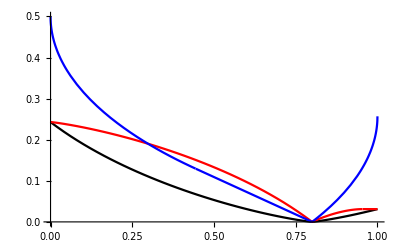

```mathematica
(* Comparing the main functions *)
Block[
(*{t=.6985},*)
{t=0.8},
Plot[{Best[s,t],Worst[s,t],Worst[t,s]},{s,0,1}, PlotStyle->{Black, Red, Blue}]
]
```

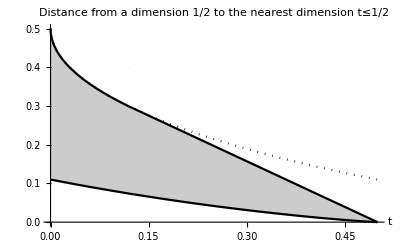

```mathematica
(* Fix s and graph the distance from a dimension s to the nearest dimension t≤s *)

Block[
(* Set the value of s and a related value *)
{s=1/2, GL=N[1-H[1-2^(s-1)]]},
Plot[{Worst[s,t],Best[s,t], HI[1-t]},{t,0,s}, PlotStyle->{Black, Black, {Black, Dotted}},Filling->{1-> {2}},AxesStyle->Thick,AxesLabel->{t,},BaseStyle->{FontSize->16},PlotLabel-> Style[StringForm["Distance from a dimension `` to the nearest dimension ``",s,t<=s],Bold],GridLines->{{GL},{}},GridLinesStyle->Directive[Thick, Dotted]]
]
```

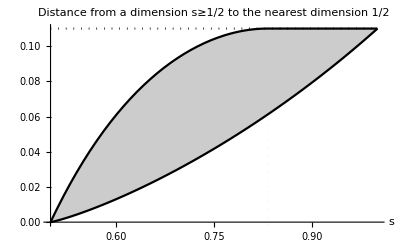

```mathematica
(* Fix t and graph the distance from a dimension s≥t to the nearest dimension t *)

Block[
(* Set the value of t and related values *)
{t=1/2, UL=N[HI[1-t]],GL = N[Log[2,1-UL]+1]},
Plot[{Worst[s,t],Best[s,t], UL},{s,t,1}, PlotStyle->{Black, Black, {Black, Dotted}},Filling->{1-> {2}},AxesStyle->Thick,AxesLabel->{s,},BaseStyle->{FontSize->16},PlotLabel-> Style[StringForm["Distance from a dimension `` to the nearest dimension ``",s>=t,t],Bold],GridLines->{{GL},{}},GridLinesStyle->Directive[Thick, Dotted]]
]
```

```mathematica
(* Entropy *)

data=Cases[Plot[H[p],{p,0,1}],Line[data_]:>data,-4,1][[1]];
Export[NotebookDirectory[]<>"Entropy.txt",data,"Table"];
```

```mathematica
(* Dimension 1 *)

data=Cases[Plot[Worst[s,1],{s,0,1}],Line[data_]:>data,-4,1][[1]];
Export[NotebookDirectory[]<>"Worst s-1.txt",data,"Table"];

data=Cases[Plot[Best[1,t],{t,0,1}],Line[data_]:>data,-4,1][[1]];
Export[NotebookDirectory[]<>"Best 1.txt",data,"Table"];
```

```mathematica
(* Dimension 1/2 *)

data=Cases[Plot[Worst[1/2,t],{t,0,1}],Line[data_]:>data,-4,1][[1]];
Export[NotebookDirectory[]<>"Worst 0.5-s.txt",data,"Table"];

data=Cases[Plot[Worst[s,1/2],{s,0,1}],Line[data_]:>data,-4,1][[1]];
Export[NotebookDirectory[]<>"Worst s-0.5.txt",data,"Table"];

data=Cases[Plot[Best[1/2,t],{t,0,1}],Line[data_]:>data,-4,1][[1]];
Export[NotebookDirectory[]<>"Best 0.5.txt",data,"Table"];
```

```mathematica
(* Dimension 0.99 *)

data=Cases[Plot[Worst[0.99,t],{t,0,1}],Line[data_]:>data,-4,1][[1]];
Export[NotebookDirectory[]<>"Worst 0.99-s.txt",data,"Table"];

data=Cases[Plot[Worst[s,0.99],{s,0,1}],Line[data_]:>data,-4,1][[1]];
Export[NotebookDirectory[]<>"Worst s-0.99.txt",data,"Table"];

data=Cases[Plot[Best[0.99,t],{t,0,1}],Line[data_]:>data,-4,1][[1]];
Export[NotebookDirectory[]<>"Best 0.99.txt",data,"Table"];
```

Part::partw: Part 1 of {} does not exist.